```mathematica
ClearAll["Global`*"]
```

```mathematica
qw=0.25 ×10^-3;
```

```mathematica
ϵo=8.85×10^-12;
```

```mathematica
Fq=(q ×qo)/(4×π×ϵo×r^2);
Fo=(m×v^2)/r;
```

```mathematica
qo=m×qw;
```

```mathematica
A=Solve[Fq==Fo,v]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-(1499.32 √q)/(√r)},{v→(1499.32 √q)/(√r)}}

```mathematica
rys1=Plot[v/.A[[2,1]]/.q->0.2 ×10^-7,{r,0.1,0.2},
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),
DisplayFunction->Identity];
rys2=Plot[v/.A[[2,1]]/.q->0.5 ×10^-7,{r,0.1,0.2},
PlotStyle->({{RGBColor[0,1,0], Thickness[0.006]}}),
DisplayFunction->Identity];
rys3=Plot[v/.A[[2,1]]/.q->1.0 ×10^-7,{r,0.1,0.2},
PlotStyle->({{RGBColor[0,0,1], Thickness[0.006]}}),
DisplayFunction->Identity];
```

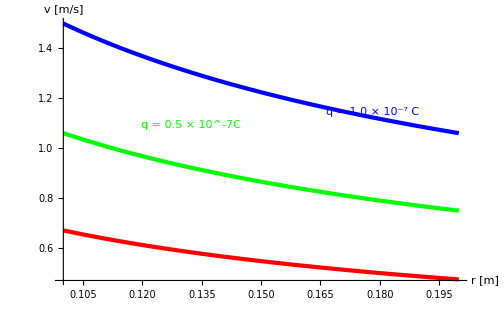

```mathematica
Show[rys1,rys2,rys3,DisplayFunction->$DisplayFunction, PlotRange ->All,
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{"r [m]","v [m/s] "},
Prolog->{Text[StyleForm["q = 0.2 × 10^-7C",FontColor->RGBColor[1,0,0]],
Scaled[{12,0.40}]],
Text[StyleForm["q = 0.5 × 10^-7C",FontColor->RGBColor[0,1,0]],
Scaled[{0.33,0.60}]],
Text[StyleForm["q = 1.0 × 10^-7 C",FontColor->RGBColor[0,0,1]],Scaled[{0.77,0.65}]]}]
```